```mathematica
u=(√(-π τ))/2 HankelH1[3/2,-k τ];
ϕ=u/(-1/H/τ);
uc=(√(-π τ))/2 HankelH2[3/2,-k τ];
ϕc=uc/(-1/H/τ);

(*Computing classicality for the case ϕϕ*)
(15  τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))/(2 σ^3 (τ1-τ2) (τ1^2+τ1 τ2+τ2^2) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4)) /.δ->0//FullSimplify;
```

```mathematica
ϕ//FunctionExpand
D[ϕ,τ]//FullSimplify//FunctionExpand
```

(ⅇ^(-ⅈ k τ) H √-τ (-ⅈ+k τ))/(√2 k √(-k τ))

-(ⅈ ⅇ^(-ⅈ k τ) H k √-τ τ)/(√2 √(-k τ))

```mathematica
C=(15  τ1^3 τ2^3 ( τ1+τ2))/(2 σ^3 (τ1^3-τ2^3)  (τ1^4+ τ1^3 τ2+ τ1^2 τ2^2+ τ1 τ2^3+τ2^4)) = (15  τ1^3 τ2^3 ( τ1+τ2))/(2 σ^3 (τ1^3-τ2^3)   ((τ1^5-τ2^5)/( τ1-τ2)))= (15  τ1^3 τ2^3 (τ1^2-τ2^2 ))/(2 σ^3 (τ1^3-τ2^3)(τ1^5-τ2^5));

C1=  (15  τ1^3 τ2^3 (τ1^2-τ2^2 ))/(2 σ^3 (τ1^3-τ2^3)(τ1^5-τ2^5))//FullSimplify
```

Set::write: Tag Times in (15 τ1^3 τ2^3 (τ1+τ2) (τ1-τ2))/(2 σ^3 (τ1^3-τ2^3) (τ1^5-τ2^5)) is Protected.

Set::write: Tag Times in (15 τ1^3 τ2^3 (τ1+τ2))/(2 σ^3 (τ1^3-τ2^3) (τ1^4+τ1^3 τ2+τ1^2 τ2^2+τ1 τ2^3+τ2^4)) is Protected.

Set::wrsym: Symbol C is Protected.

```mathematica
(15  τ1^3 τ2^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/(2 σ^3 (τ1^3 -τ2^3)((1-δ)^5 τ1^5-(1+δ)^5 τ2^5)) /.δ->0//FullSimplify
```

(15 τ1^3 τ2^3 (τ1+τ2))/(2 σ^3 (τ1^2+τ1 τ2+τ2^2) (τ1^5-τ2^5))

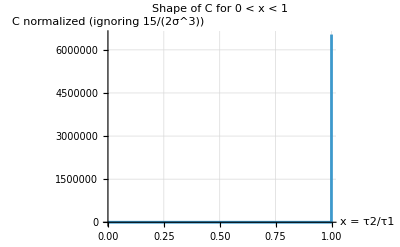

```mathematica
f[x_]:=(x^3*(1+x))/((1+x+x^2)*(1-x^5))
Plot[f[x],{x,0,1},AxesLabel->{"x = τ2/τ1","C normalized (ignoring 15/(2σ^3))"},PlotRange->All,GridLines->Automatic,PlotLabel->"Shape of C for 0 < x < 1"]
```

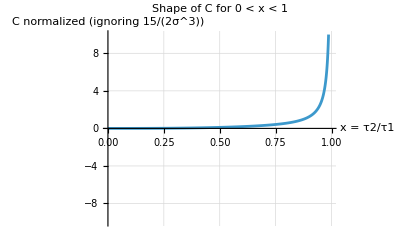

```mathematica
f[x_]:=(x^3*(1+x))/((1+x+x^2)*(1-x^5))
Plot[f[x],{x,0,1},AxesLabel->{"x = τ2/τ1","C normalized (ignoring 15/(2σ^3))"},PlotRange->10,GridLines->Automatic,PlotLabel->"Shape of C for 0 < x < 1"]
```

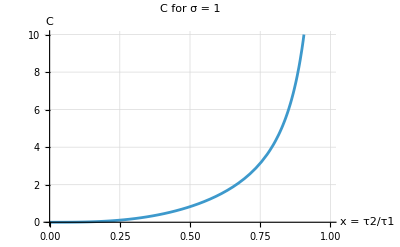

```mathematica
sigma=1;
Cval[x_]:=(15/(2*sigma^3))*(x^3*(1+x))/((1+x+x^2)*(1-x^5))
Plot[Cval[x],{x,0,1},AxesLabel->{"x = τ2/τ1","C"},PlotRange->{{0,1},{0,10}},GridLines->Automatic,PlotLabel->"C for σ = 1"]
```

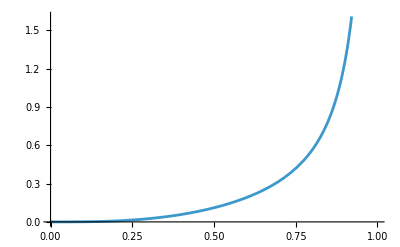

```mathematica
expr=x^2-3 x+1;
Plot[Abs[x^3(1-x^2)/((1-x^3)(1-x^5))],{x,0,1}]
```

```mathematica
Plot[x^3(1-x^2)/((1-x^3)(1-x^5)),{x,0,1}]
```

-Graphics-

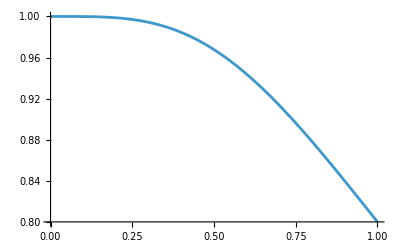

```mathematica
Plot[Abs[(1-x^4)/(1-x^5)],{x,0,1}]
```

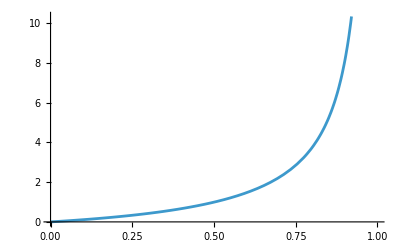

```mathematica
Plot[Abs[x(1-x^6)/(1-x)/(1-x^7)],{x,0,1}]
```

```mathematica
ϕvintegral=1/(16 π^2 δ^2 σ^2 (τ1-τ2)^5)H^2 τ1 (ⅈ τ1 (-ⅇ^(-ⅈ k1 (τ1-τ2)) (24 ⅈ+k1 (-24+k1 (-12 ⅈ+k1 (4+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (24 ⅈ+k2 (-24+k2 (-12 ⅈ+k2 (4+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)))+(ⅇ^(-ⅈ k1 (τ1-τ2)) (6-k1 (-6 ⅈ+k1 (3+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (-6+k2 (-6 ⅈ+k2 (3+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))) (τ1-τ2)) τ2^2/.{k1->-σ/τ2(1-δ),k2->-σ/τ1(1+δ)}//Simplify
X= Series[ϕvintegral, {σ,0,3}]
```

1/(16 π^2 δ^2 σ^2 τ1^2 (τ1-τ2)^5 τ2^2)H^2 (-((τ1-τ2) τ2 (ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (6 τ1^3-(1+δ) σ (6 ⅈ τ1^2+(1+δ) σ (3 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) τ2^3-ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) τ1^3 (6 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-3 τ2) (τ1-τ2)-6 ⅈ τ2^2))))+ⅈ (ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (24 ⅈ τ1^4+(1+δ) σ (24 τ1^3-(1+δ) σ (12 ⅈ τ1^2+(1+δ) σ (4 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) τ2^4-ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) τ1^4 (24 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (24 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-4 τ2) (τ1-τ2)-12 ⅈ τ2^2)))))

(H^2 (-((-1+δ)^4 τ1^3 (τ1-τ2)^4)/(4 τ2)+((1+δ)^4 (τ1-τ2)^4 τ2^3)/(4 τ1)) σ^2)/(16 π^2 δ^2 τ1^2 (τ1-τ2)^4 τ2)-(ⅈ H^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5) σ^3)/(80 π^2 δ^2 τ1^4 τ2^2)+O[σ]^4

```mathematica
X= Series[ϕvintegral, {σ,0,4}]
```

(H^2 (-((-1+δ)^4 τ1^3 (τ1-τ2)^4)/(4 τ2)+((1+δ)^4 (τ1-τ2)^4 τ2^3)/(4 τ1)) σ^2)/(16 π^2 δ^2 τ1^2 (τ1-τ2)^4 τ2)-(ⅈ H^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5) σ^3)/(80 π^2 δ^2 τ1^4 τ2^2)-((H^2 (τ1-τ2) (τ1+τ2) (τ1^6-6 δ τ1^6+15 δ^2 τ1^6-20 δ^3 τ1^6+15 δ^4 τ1^6-6 δ^5 τ1^6+δ^6 τ1^6-τ2^6-6 δ τ2^6-15 δ^2 τ2^6-20 δ^3 τ2^6-15 δ^4 τ2^6-6 δ^5 τ2^6-δ^6 τ2^6)) σ^4)/(192 (π^2 δ^2 τ1^5 τ2^4))+O[σ]^5

```mathematica
Y = Series[1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 τ2^2 (1/τ1^5 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (120 τ1^5-(1+δ) σ (120 ⅈ τ1^4+(1+δ) σ (60 τ1^3-(1+δ) σ (20 ⅈ τ1^2+(1+δ) σ (5 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))-1/τ2^5 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (120 τ2^5-(1-δ) σ (τ1-τ2) (120 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (60 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-5 τ2) (τ1-τ2)-20 ⅈ τ2^2))))), {σ,0,5}]//FullSimplify
```

-((H^2 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6)) σ^4)/(96 (π^2 δ^2 τ1^4 τ2^4))+(ⅈ H^2 τ1^2 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^2 σ^5)/(112 π^2 δ^2)+O[σ]^6

```mathematica
Q=(2 σ^3 (τ1^3-τ2^3))/(15 τ1^3 τ2^3) ((T1^4+T1^3 T2+T1^2 T2^2+T1 T2^3+T2^4)/(T1 +T2))
1/Q
```

(2 (T1^4+T1^3 T2+T1^2 T2^2+T1 T2^3+T2^4) σ^3 (τ1^3-τ2^3))/(15 (T1+T2) τ1^3 τ2^3)

(15 (T1+T2) τ1^3 τ2^3)/(2 (T1^4+T1^3 T2+T1^2 T2^2+T1 T2^3+T2^4) σ^3 (τ1^3-τ2^3))

```mathematica
(15 τ1^3 τ2^3)/(2 σ^3 (τ1^3-τ2^3))((T1^2-T2^2)/(T1^5-T2^5))/.{T1->(1-δ),T2->(1+δ)x,τ1->1,τ2->x}
```

(15 x^3 ((1-δ)^2-x^2 (1+δ)^2))/(2 (1-x^3) ((1-δ)^5-x^5 (1+δ)^5) σ^3)

```mathematica
Clear[δ]
```

```mathematica
(15 x^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/(2 (1-x^3) σ^3 ((1-δ)^5 τ1^5-(1+δ)^5 τ2^5))

Plot[(x^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/((1-x^3)((1-δ)^5 τ1^5-(1+δ)^5 τ2^5)), {x,0,(1-δ)/(1+δ)}],δ->.1
```

(15 x^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/(2 (1-x^3) σ^3 ((1-δ)^5 τ1^5-(1+δ)^5 τ2^5))

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,0,(1-δ)/(1+δ)} is not a machine-sized real number.

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,0,(1-δ)/(1+δ)} is not a machine-sized real number.

Sequence[Plot[(x^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/((1-x^3) ((1-δ)^5 τ1^5-(1+δ)^5 τ2^5)),{x,0,(1-δ)/(1+δ)}],δ→0.1]

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

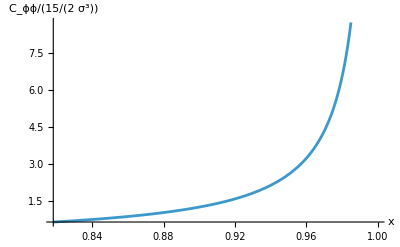

```mathematica
Sequence[Plot[(x^3 ((1-δ)^2 τ1^2-(1+δ)^2 τ2^2))/((1-x^3) ((1-δ)^5 τ1^5-(1+δ)^5 τ2^5)),{x,0,(1-δ)/(1+δ)}],δ->0.1]
(*-----------------------------------------------------------------------------------------------------------------------------*)
Plot[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)), {x,(1-δ)/(1+δ),1},AxesLabel->{Style[TraditionalForm[x],16],Style[TraditionalForm[HoldForm[Subscript[C,ϕϕ]/((15/(2 σ^3)))]],16]}]/.δ->.1
```

{pdfLaTeX→C:\Users\Melika\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe}

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

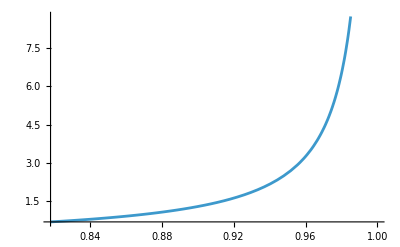

```mathematica
ConfigureMaTeX["Ghostscript"->"C:/Program Files/gs/gs10.07.1/bin/gswin64c.exe"]

Plot[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)),{x,(1-δ)/(1+δ),1},AxesLabel->{MaTeX["x",Magnification->1.2],MaTeX["\\frac{C_{\\phi\\phi}}{15/2\\sigma^3}",Magnification->1.2]}]/. δ->.1
```

```mathematica
Manipulate[Plot[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)),{x,(1-δ)/(1+δ),1},AxesLabel->{Style[TraditionalForm[x],16],Style[TraditionalForm[HoldForm[Subscript[C,ϕϕ]/(15/(2 σ^3))]],16]}],{{δ,0.1,"δ"},0.001,0.9,0.01}]
```

```mathematica
Manipulate[Plot[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)), {x,(1-δ)/(1+δ),1}],{δ,0,1}]
```

```mathematica
Limit[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)), x->(1-δ)/(1+δ)]//FullSimplify
```

1/(15 δ+5 δ^3)

```mathematica
C2= (τ1 (T1^4-T2^4))/(T1^5-T2^5)/.{T1->(1-δ),T2->(1+δ)x,τ1->1,τ2->x}
```

((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)

```mathematica
((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)/.x->1//FullSimplify
```

(4 (1+δ^2))/(5+10 δ^2+δ^4)

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

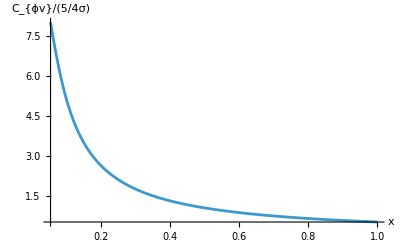

```mathematica
Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)], {x,(1-δ)/(1+δ),1},PlotRange->All,AxesLabel->{"x","C_{ϕv}/(5/4σ)"}]/.δ->.9
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

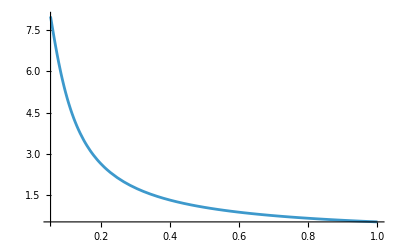

```mathematica
Needs["MaTeX`"]

Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)],{x,(1-δ)/(1+δ),1},PlotRange->All,AxesLabel->{MaTeX["x",Magnification->1.2],MaTeX["\\frac{C_{\\phi v}}{5/(4\\sigma)}",Magnification->1.2]}]/. δ->.9
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

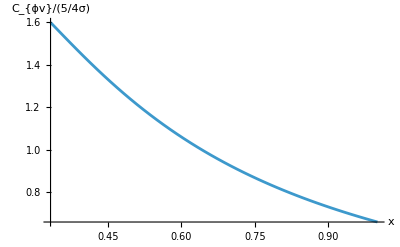

```mathematica
Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)], {x,(1-δ)/(1+δ),1},PlotRange->All,AxesLabel->{"x","C_{ϕv}/(5/4σ)"}]/.δ->.5
```

```mathematica
Manipulate[Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)], {x,(1-δ)/(1+δ),1}],{δ,0,1}]
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

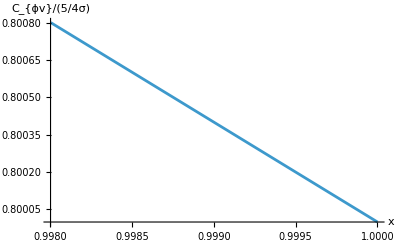

```mathematica
Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)], {x,(1-δ)/(1+δ),1},PlotRange->All,AxesLabel->{"x","C_{ϕv}/(5/4σ)"}]/.δ->.001
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

General::prng: Value of option PlotRange -> All AxesLabel→{x,(4 C_(v ϕ))/(5 σ)} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

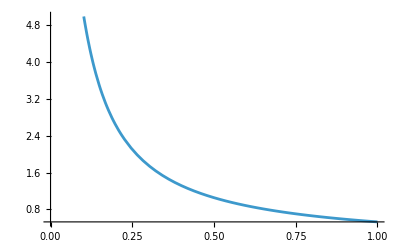

```mathematica
Plot[Abs[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5)],{x,(1-δ)/(1+δ),1},PlotRange->All  AxesLabel->{Style[TraditionalForm[x],16],Style[TraditionalForm[Subscript[C," v""ϕ"]/((5/4) σ)],16]}]/. δ->.9
```

```mathematica
Limit[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5), x->(1-δ)/(1+δ)]//FullSimplify
```

4/(5-5 δ)

```mathematica
Limit[((1-δ)^4-x^4 (1+δ)^4)/((1-δ)^5-x^5 (1+δ)^5), x->1]//FullSimplify
```

(4 (1+δ^2))/(5+10 δ^2+δ^4)

```mathematica
C3 = (τ1 τ2 (T1^6-T2^6))/((τ1 - τ2)(T1^7-T2^7))/.{T1->(1-δ),T2->(1+δ)x,τ1->1,τ2->x}
```

(-4+8 δ-8 δ^3+4 δ^4)/(-5+15 δ-10 δ^2-10 δ^3+15 δ^4-5 δ^5)

(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

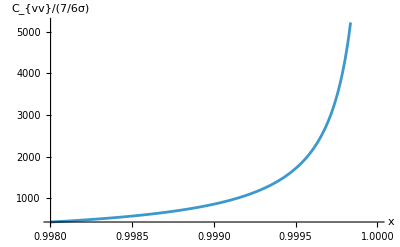

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

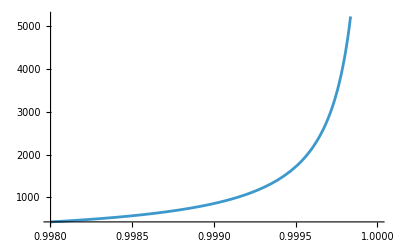

```mathematica
Plot[Abs[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))], {x,(1-δ)/(1+δ),1},AxesLabel->{"x","C_{vv}/(7/6σ)"}]/.δ->.001
Needs["MaTeX`"]

Plot[Abs[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))],{x,(1-δ)/(1+δ),1},AxesLabel->{MaTeX["x"],MaTeX["\\frac{C_{vv}}{7/(6\\sigma)}"]}]/. δ->.001
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

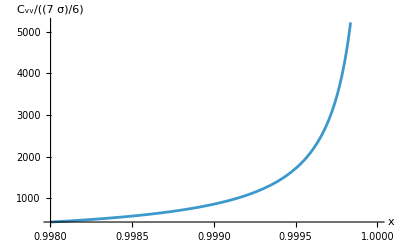

```mathematica
Plot[Abs[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))], {x,(1-δ)/(1+δ),1},AxesLabel->{Style[TraditionalForm[x],16],Style[TraditionalForm[HoldForm[Subscript[C,vv]/((7/6) σ)]],16]}]/.δ->.001
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

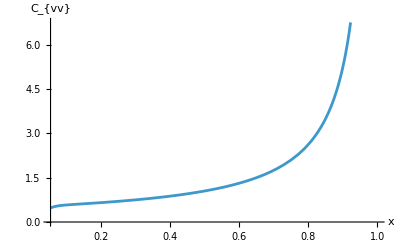

```mathematica
Plot[Abs[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))], {x,(1-δ)/(1+δ),1},AxesLabel->{"x","C_{vv}"}]/.δ->.9
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

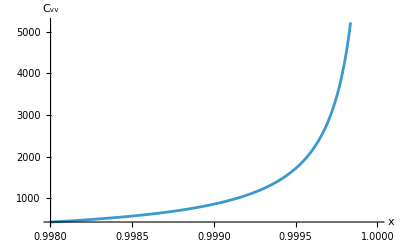

```mathematica
Plot[Abs[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7))],{x,(1-δ)/(1+δ),1},AxesLabel->{Style[TraditionalForm[x],16],Style[TraditionalForm[Subscript[C,vv]],16]}]/. δ->.001
```

```mathematica
Limit[(x ((1-δ)^6-x^6 (1+δ)^6))/((1-x) ((1-δ)^7-x^7 (1+δ)^7)),x->(1-δ)/(1+δ)]//FullSimplify
```

3/(7 δ)

```mathematica
,AxesLabel->{"k","W"}
```

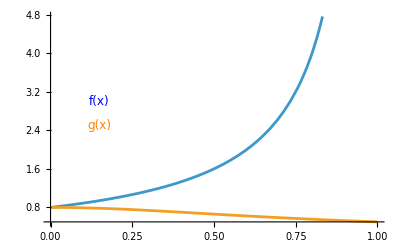

```mathematica
Plot[{4/(5 (1-x)),(4 (1+x^2))/(5+10 x^2+x^4)},{x,0,1},Epilog->{Text[Style["f(x)",Blue,12],{0.15,3}],Text[Style["g(x)",Orange,12],{0.15,2.5}]}]
```

```mathematica
Plot[(x^3 ((1-δ)^2-x^2 (1+δ)^2))/((1-x^3) ((1-δ)^5-x^5 (1+δ)^5)), {x,(1-δ)/(1+δ),1}AxesLabel->{"x","C_{ϕϕ}"}]/.δ->.9
```

Plot::pllim: Range specification {x,(1-δ)/(1+δ),1} AxesLabel→{x,C_{ϕϕ}} is not of the form {x, xmin, xmax}.

Plot::pllim: Range specification {x,(1-0.9)/(1+0.9),1} AxesLabel→{x,C_{ϕϕ}} is not of the form {x, xmin, xmax}.

Plot[(x^3 ((1-0.9)^2-x^2 (1+0.9)^2))/((1-x^3) ((1-0.9)^5-x^5 (1+0.9)^5)),{x,(1-0.9)/(1+0.9),1} AxesLabel→{x,C_{ϕϕ}}]

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

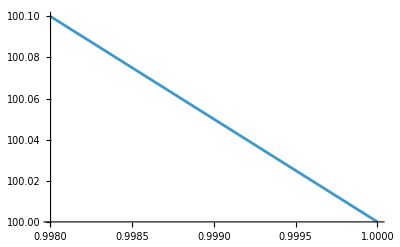

```mathematica
Plot[Abs[(125(1-x^4 ))/(x^5 -1)], {x,(1-δ)/(1+δ),1},PlotRange->All]/.δ->.001
```

Plot::plln: Limiting value (1-δ)/(1+δ) in {x,(1-δ)/(1+δ),1} is not a machine-sized real number.

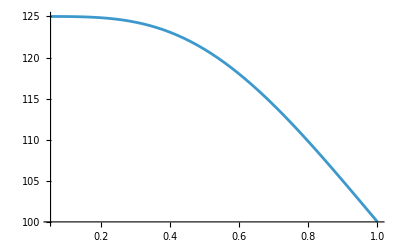

```mathematica
Plot[Abs[(125(1-x^4 ))/(x^5 -1)], {x,(1-δ)/(1+δ),1},PlotRange->All]/.δ->.9
```

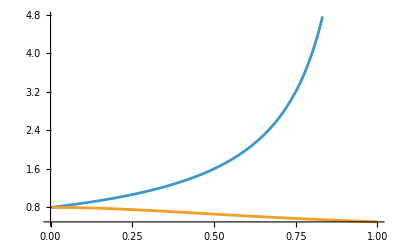

```mathematica
Needs["MaTeX`"]

Plot[{4/(5 (1-x)),(4 (1+x^2))/(5+10 x^2+x^4)},{x,0,1},AxesLabel->{MaTeX["\delta"],MaTeX["\\frac{C_{\\phi v}}{5/(4\\sigma)}"]}]
```